```mathematica
dim=8;
Clear[μ,η];
A[6]=B[6]=μ;
A[7]=B[7]=η;
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x0*x3+x1*x4)/2)*η^(-(x1+x3)/2)*Exp[-2*A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/2)*B[4]^(-(x0*x4)/2)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0<=1,x0+=2,
For[x2=-1,x2<=1,x2+=2,
For[x4=-1,x4<=1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
(*Equates the unrenormalized with the renormalized variables*)
req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4] == leq[4];
req[5] ==leq[5] ;
req[6] ==leq[6] ;
req[7] ==leq[7] ;
SB[0]=Simplify[Solve[Simplify[(Factor[leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7]])^(-1/8),Assumptions->B[0]>0]==Simplify[(Factor[req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7]])^(-1/8),Assumptions->η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0],B[0]],Assumptions->C[1]==0&&η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0][[1]];
SB[0]={B[0]-> 2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0&& B[2]>0&& B[4]>0&& B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0 && B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0 && B[5]>0 && B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[5]],1]];
SBT=Table[Part[Factor[SB[n]],1],{n,0,5}];
```

```mathematica
(* Set up Initial values(SIC),Initial Step, RG steps, W, Z1, LnZ1, DLnZ1, and constants*)
Clear[μ,η]
SIC={B[0]->0,B[1]->η,B[2]->η,B[3]->μ,B[4]->1,B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
W=Table[Factor[D[(B[i]/.SBT),A[j]]],{j,0,dim-1},{i,0,dim-1}];
InitRGW:=Block[{},
InitRG;
Υ=Array[KroneckerDelta,{dim,dim}];
];
RGW:=Block[{},
Υ=Together[Υ.(W/.SAT)];
RG;
];
LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
DLnZ1=Table[Factor[D[LnZ1,A[i]]],{i,0,dim-1}];
InitRGW;
dμdβ=-4μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
```

```mathematica
SIC
Table[D[A[i]/.SAT,μ],{i,0,dim-1}]
dA0dμ
Table[D[A[i]/.SAT,η],{i,0,dim-1}]
dA0dη
```

{B[0]→0,B[1]→η,B[2]→η,B[3]→μ,B[4]→1,B[5]→1}

{0,0,0,1,0,0,1,0}

{0,0,0,-4 μ,0,0,-4 μ,0}

{0,1,1,0,0,0,0,1}

{0,-2 η,-2 η,0,0,0,0,-2 η}

```mathematica
(*****AFM One Point Function*****)
(** Magnetization vs H at different μ **)
```

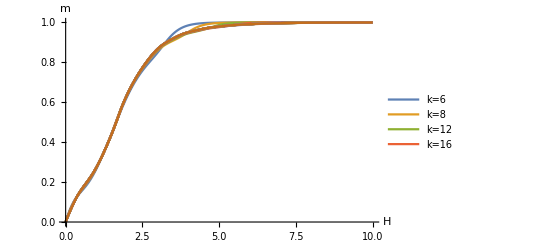

```mathematica
(*μ=7.389*)
Clear[μ,η]
InitRGW;
precN=1000;
kVector={6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,32,64,100,128,200,256};
(***** Mag vs H at different μ*****)
Clear[μ,η];
InitRGW;
μ=N[7.389,100];(*1:high T;1000:low T*)y=1;
Hmin=0;
Hmax=10;
Hinc=0.05;
HVector=Range[Hmin,Hmax,Hinc];
ηmax=Exp[-Hmin];
ηmin=Exp[-Hmax];
ηVector=Exp[-HVector];
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];(*Magnetization at different H at μ=0.01*)InitRGW;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[i=1,i≤Dimensions[HVector][[1]],++i,
Clear[η];
kind=1;
InitRGW;
η=ηVector[[i]];
For[j=3,j≤Max[kVector],++j,RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],Part[Part[MagH,kind],i]=1.0/(2^(j+1.0)+1)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,];];];
ListLinePlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=8","k=12","k=16"},AxesOrigin->{0.0,0.0},AxesLabel->{H,m}]
MagHc=MagH;
PrependTo[MagHc,HVector];
PrependTo[MagHc,ηVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
MagHc=Transpose[MagHc];
MagHc=PrependTo[MagHc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magH_7d389.csv",MagHc];
```

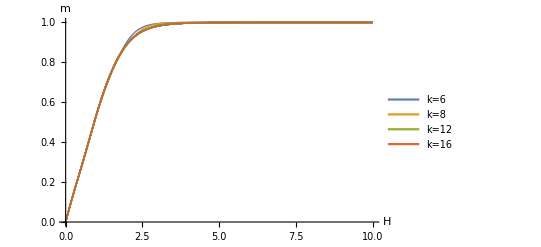

```mathematica
(*μ=3*)
Clear[μ,η]
InitRGW;
precN=1000;
kVector={6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,32,64,100,128,200,256};
Clear[μ,η];
InitRGW;
μ=N[3.0,1000];(*1:high T;1000:low T*)y=1;
Hmin=0;
Hmax=10;
Hinc=0.01;
HVector=Range[Hmin,Hmax,Hinc];
ηmax=Exp[-Hmin];
ηmin=Exp[-Hmax];
ηVector=Exp[-HVector];
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];(*Magnetization at different H at μ=0.01*)InitRGW;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[i=1,i≤Dimensions[HVector][[1]],++i,Clear[η];
kind=1;
InitRGW;
η=ηVector[[i]];
For[j=3,j≤Max[kVector],++j,RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],Part[Part[MagH,kind],i]=1.0/(2^(j+1.0)+1)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,];];];
ListLinePlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=8","k=12","k=16"},AxesOrigin->{0.0,0.0},AxesLabel->{H,m}]
MagHc=MagH;
PrependTo[MagHc,HVector];
PrependTo[MagHc,ηVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
MagHc=Transpose[MagHc];
MagHc=PrependTo[MagHc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magH_m3.csv",MagHc];
```

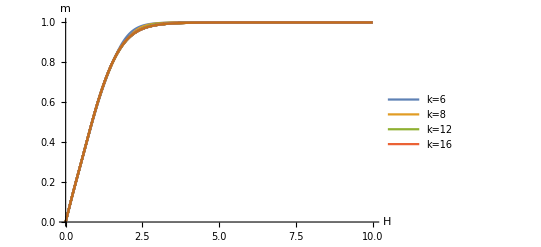

```mathematica
(*μ=2.718282* {1E9,54.6,7.389,3,2.718282,1.492,1.00000002}**)
Clear[μ,η]
InitRGW;
precN=1000;
kVector={6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,32,64,100,128,200,256};
Clear[μ,η];
InitRGW;
μ=N[2.718282,100];(*1:high T;1000:low T*)y=1;
Hmin=0;
Hmax=10;
Hinc=0.02;
HVector=Range[Hmin,Hmax,Hinc];
ηmax=Exp[-Hmin];
ηmin=Exp[-Hmax];
ηVector=Exp[-HVector];
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];(*Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[i=1,i≤Dimensions[HVector][[1]],++i,
Clear[η];
kind=1;
InitRGW;
η=ηVector[[i]];
For[j=3,j≤Max[kVector],++j,RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],Part[Part[MagH,kind],i]=1.0/(2^(j+1.0)+1)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,];];];
ListLinePlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=8","k=12","k=16"},AxesOrigin->{0.0,0.0},AxesLabel->{H,m}]
MagHc=MagH;
PrependTo[MagHc,HVector];
PrependTo[MagHc,ηVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
MagHc=Transpose[MagHc];
MagHc=PrependTo[MagHc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magH_m2d718.csv",MagHc];
```

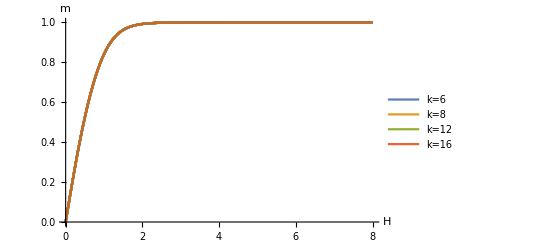

```mathematica
(*μ=1.492* {1E9,54.6,7.389,3,2.718282,1.492,1.00000002}**)
Clear[μ,η]
InitRGW;
precN=1000;
kVector={6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,32,64,100,128,200,256};
Clear[μ,η];
InitRGW;
μ=N[1.492,100];(*1:high T;1000:low T*)y=1;
Hmin=0;
Hmax=8;
Hinc=0.02;
HVector=Range[Hmin,Hmax,Hinc];
ηmax=Exp[-Hmin];
ηmin=Exp[-Hmax];
ηVector=Exp[-HVector];
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];(*Magnetization at different H at μ=0.01*)InitRGW;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[i=1,i≤Dimensions[HVector][[1]],++i,Clear[η];
kind=1;
InitRGW;
η=ηVector[[i]];
For[j=3,j≤Max[kVector],++j,RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],Part[Part[MagH,kind],i]=1.0/(2^(j+1.0)+1)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,];];];
ListLinePlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=8","k=12","k=16"},AxesOrigin->{0.0,0.0},AxesLabel->{H,m}]
MagHc=MagH;
PrependTo[MagHc,HVector];
PrependTo[MagHc,ηVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
MagHc=Transpose[MagHc];
MagHc=PrependTo[MagHc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magH_m1d492.csv",MagHc];
```

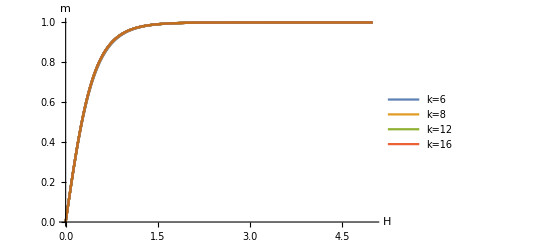

```mathematica
(*μ=1.00000002* {1E9,54.6,7.389,3,2.718282,1.492,1.00000002}**)
Clear[μ,η]
InitRGW;
precN=1000;
kVector={6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,32,64,100,128,200,256};
Clear[μ,η];
InitRGW;
μ=N[1.00000002,100];(*1:high T;1000:low T*)y=1;
Hmin=0;
Hmax=5;
Hinc=0.01;
HVector=Range[Hmin,Hmax,Hinc];
ηmax=Exp[-Hmin];
ηmin=Exp[-Hmax];
ηVector=Exp[-HVector];
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];(*Magnetization at different H at μ=0.01*)InitRGW;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[i=1,i≤Dimensions[HVector][[1]],++i,Clear[η];
kind=1;
InitRGW;
η=ηVector[[i]];
For[j=3,j≤Max[kVector],++j,RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],Part[Part[MagH,kind],i]=1.0/(2^(j+1.0)+1)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,];];];
ListLinePlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=8","k=12","k=16"},AxesOrigin->{0.0,0.0},AxesLabel->{H,m}]
MagHc=MagH;
PrependTo[MagHc,HVector];
PrependTo[MagHc,ηVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
MagHc=Transpose[MagHc];
MagHc=PrependTo[MagHc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magH_m1d00000002.csv",MagHc];
```

```mathematica
(***** Constants for IE: Internal Energy*****)
Clear[μ,η]
InitRGW;
(**Temperature for Mag, IE**)
precN=1000;
Tmin=0.011;
Tmax=10.006;
Tinc=0.05;
TVector=N[Prepend[Range[Tmin,Tmax,Tinc],0.01],precN];
μVector=Exp[2/TVector];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*100]/100.0,1,0.01];
μinvVector=N[Join[μinvVector, μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μiv[[Dimensions[μiv][[1]]]]=N[0.99999998,10];
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
Clear[μiv];
kVector={6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,32,64,100,128,200,256};
Clear[μ,η,y];
InitRGW;
dμdβ=-4 μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
η=N[1.0,precN];
IE=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[TVector][[1]]}];
μind=0;
Do[kind=1;
μind++;
Clear[μ];
InitRGW;
μ=N[μVector[[μind]],precN];
For[i=3,i≤Max[kVector],++i,RGW;
If[i==kVector[[kind]],Part[Part[IE,kind],μind]=1/2^(i)*(dA0dμ.Υ).(DLnZ1/.SAT);kind++,];],
{Tx,Tmin,(Tmin+Tinc*(Dimensions[μVector][[1]]-1)),Tinc}
];
Rasterize[ListLinePlot[Table[Table[{1.0/μVector[[i]],IE[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=12","k=16","k=24"},PlotStyle->Thick]]
IEc=IE;
PrependTo[IEc,TVector];
PrependTo[IEc,1.0/μVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
IEc=Transpose[IEc];
IEc=PrependTo[IEc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_IE_test2.csv",IEc];
```

-Graphics-

Export::nodir: Directory "/home/xcheng0907/C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/" does not exist.

OpenWrite::noopen: Cannot open "/home/xcheng0907/C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_IE_test2.csv".

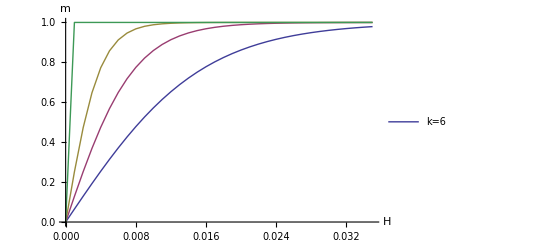

```mathematica
(***** Constants for magnetization: <m> vs H*****)
Clear[μ,η];
InitRGW;
Hmin=0.0;
Hmax=0.035;
Hinc=0.001;
HVector=Range[Hmin,Hmax,Hinc];
ηmax=Exp[-2*Hmin];
ηmin=Exp[-2*Hmax];
ηVector=Exp[-2*HVector];
kVector={6,7,8,16};
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
μ=0.01;
For[i=1,i≤Dimensions[HVector][[1]],++i,
Clear[η];
kind=1;
InitRGW;
η=ηVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[MagH,kind],i]=1.0/(2^j+1.0)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[MagH][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6"},AxesOrigin->{0.0,0.0},AxesLabel->{H,m} ]
```

```mathematica
(**************<m> vs μ at different H  *********************)
(**Temperature for Mag, IE**)
precN=1000;
Tmin=0.011;
Tmax=10.006;
Tinc=0.005;
TVector=N[Prepend[Range[Tmin,Tmax,Tinc],0.01],precN];
μVector=Exp[2/TVector];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,1,0.005];
μinvVector=N[Join[μinvVector, μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μiv[[Dimensions[μiv][[1]]]]=N[0.99999998,10];
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
Clear[μiv]
```

```mathematica
(*H=1e-2*)
H=1/10^2;
Clear[μ,η,Magμc];
InitRGW;
dηdH=-2 η;
kind=1;
kVector=Range[6,128,1]; (*Range[6,128,1];*)
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=N[Exp[-H],precN];
Print["H=",N[H,6]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=N[μVector[[i]],precN];
For[j=3,j≤Max[kVector],++j,
RGW;
If[j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT);
++kind,
];
];
];
ListLinePlot[Table[Table[{μinvVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{"1/μ","m"},PlotRange->Full]
Magμc=Magμ;
PrependTo[Magμc,TVector];
PrependTo[Magμc,N[μVector,25]];
PrependTo[kVector,0];
PrependTo[kVector,0];
Magμc=Transpose[Magμc];
Magμc=PrependTo[Magμc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magT_H1e-2.csv",Magμc];
```

H=0.01

-Graphics-

```mathematica
(*H=1e-4*)
H=1/10^4;
Clear[μ,η,Magμc];
InitRGW;
dηdH=-2 η;
kind=1;
kVector=Range[6,128,1]; (*Range[6,128,1];*)
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=N[Exp[-H],precN];
Print["H=",N[H,6]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=N[μVector[[i]],precN];
For[j=3,j≤Max[kVector],++j,
RGW;
If[j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT);
++kind,
];
];
];
ListLinePlot[Table[Table[{μinvVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{"1/μ","m"},PlotRange->Full]
Magμc=Magμ;
PrependTo[Magμc,TVector];
PrependTo[Magμc,N[μVector,25]];
PrependTo[kVector,0];
PrependTo[kVector,0];
Magμc=Transpose[Magμc];
Magμc=PrependTo[Magμc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magT_H1e-4.csv",Magμc];
```

H=0.0001

-Graphics-

```mathematica
(*H=1e-6*)
H=1/10^6;
Clear[μ,η,Magμc];
InitRGW;
dηdH=-2 η;
kind=1;
kVector=Range[6,128,1]; (*Range[6,128,1];*)
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=N[Exp[-H],precN];
Print["H=",N[H,6]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=N[μVector[[i]],precN];
For[j=3,j≤Max[kVector],++j,
RGW;
If[j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT);
++kind,
];
];
];
ListLinePlot[Table[Table[{μinvVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{"1/μ","m"},PlotRange->Full]
Magμc=Magμ;
PrependTo[Magμc,TVector];
PrependTo[Magμc,N[μVector,25]];
PrependTo[kVector,0];
PrependTo[kVector,0];
Magμc=Transpose[Magμc];
Magμc=PrependTo[Magμc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magT_H1e-6.csv",Magμc];
```

H=1.×10^-6

-Graphics-

```mathematica
(*H=1e-8*)
H=1/10^8;
Clear[μ,η,Magμc];
InitRGW;
dηdH=-2 η;
kind=1;
kVector=Range[6,128,1]; (*Range[6,128,1];*)
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=N[Exp[-H],precN];
Print["H=",N[H,6]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=N[μVector[[i]],precN];
For[j=3,j≤Max[kVector],++j,
RGW;
If[j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT);
++kind,
];
];
];
ListLinePlot[Table[Table[{μinvVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{"1/μ","m"},PlotRange->Full]
Magμc=Magμ;
PrependTo[Magμc,TVector];
PrependTo[Magμc,N[μVector,25]];
PrependTo[kVector,0];
PrependTo[kVector,0];
Magμc=Transpose[Magμc];
Magμc=PrependTo[Magμc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magT_H1e-8.csv",Magμc];
```

H=1.×10^-8

-Graphics-

```mathematica
(*H=1e-10*)
H=1/10^10;
Clear[μ,η,Magμc];
InitRGW;
dηdH=-2 η;
kind=1;
kVector=Range[6,128,1]; (*Range[6,128,1];*)
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=N[Exp[-H],precN];
Print["H=",N[H,6]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=N[μVector[[i]],precN];
For[j=3,j≤Max[kVector],++j,
RGW;
If[j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT);
++kind,
];
];
];
ListLinePlot[Table[Table[{μinvVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{"1/μ","m"},PlotRange->Full]
Magμc=Magμ;
PrependTo[Magμc,TVector];
PrependTo[Magμc,N[μVector,25]];
PrependTo[kVector,0];
PrependTo[kVector,0];
Magμc=Transpose[Magμc];
Magμc=PrependTo[Magμc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magT_H1e-10.csv",Magμc];
```

H=1.×10^-10

-Graphics-

```mathematica
(*H=1e-12*)
H=1/10^12;
Clear[μ,η,Magμc];
InitRGW;
dηdH=-2 η;
kind=1;
kVector=Range[6,128,1]; (*Range[6,128,1];*)
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=N[Exp[-H],precN];
Print["H=",N[H,6]];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=N[μVector[[i]],precN];
For[j=3,j≤Max[kVector],++j,
RGW;
If[j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT);
++kind,
];
];
];
ListLinePlot[Table[Table[{μinvVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{"1/μ","m"},PlotRange->Full]
Magμc=Magμ;
PrependTo[Magμc,TVector];
PrependTo[Magμc,N[μVector,25]];
PrependTo[kVector,0];
PrependTo[kVector,0];
Magμc=Transpose[Magμc];
Magμc=PrependTo[Magμc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magT_H1e-12.csv",Magμc];
```

H=1.×10^-12

-Graphics-

1/ⅇ^(1/100000)=0.99999000004999983333374999916666805555357143105158

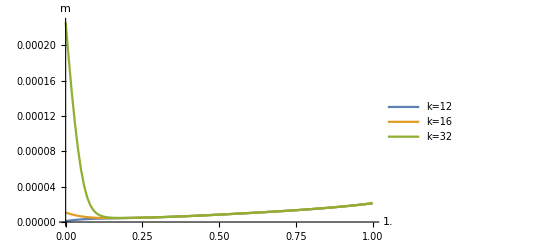

```mathematica
Clear[μ,η,y];
y=0;
InitRGW;
dηdH=-2 η;
kind=3;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-1/10^5];
Print[η,"=",N[η,50]];
For[i=1,i≤Dimensions[μVector][[1]],++i,Clear[μ];
InitRGW;
μ=μVector[[i]];
For[j=3,j≤kVector[[kind]],++j,RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],Part[Part[Magμ,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT),];];];
ListLinePlot[Table[Table[{μinvVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=12","k=16","k=32","k=64"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full]
```

1/ⅇ^(1/100000)=0.99999000004999983333374999916666805555357143105158

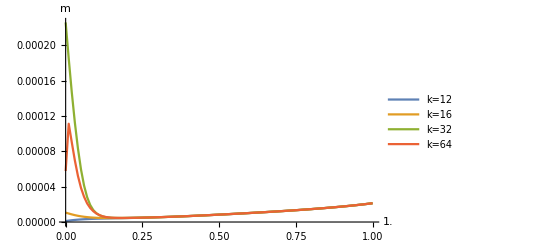

```mathematica
Clear[μ,η,y];
y=0;
InitRGW;
dηdH=-2 η;
kind=4;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-1/10^5];
Print[η,"=",N[η,50]];
For[i=1,i≤Dimensions[μinvVector][[1]],++i,Clear[μ];
InitRGW;
μ=μVector[[i]];
For[j=3,j≤kVector[[kind]],++j,RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],Part[Part[Magμ,kind],i]=1/(2^(j+1))*(dA0dη.Υ).(DLnZ1/.SAT),];];];
ListLinePlot[Table[Table[{μinvVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=12","k=16","k=32","k=64"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m},PlotRange->Full]
```

```mathematica
(**************<m> vs Log(H) given ks to find 'Z2' broken H *********************)
```

```mathematica
(*μ=7.389*)
Clear[μ,η,MagHc];
precN=1000;(*1000*)
HVector=N[10^Range[0,-128,-1],precN];(*N[10^(Range[-1,-128,-1]),precN];*)
ηVector=N[Exp[-HVector],precN];
kVector=Range[6,128,1]; (*Range[6,128,1];*)
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];
InitRGW;
dηdH=-2 η;
kind=1;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[i=1,i≤Dimensions[HVector][[1]],++i,
Clear[η,];
kind=1;
InitRGW;
μ=N[7.389,precN];
η=ηVector[[i]];
For[j=3,j≤Max[kVector],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[MagH,kind],i]=1.0/(2^(j+1.0)+1)*(dA0dη.Υ).(DLnZ1/.SAT);
kind++,
];
];
];
ListLogLogPlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=7","k=8","k=9"},AxesOrigin->{0.0,0.0},Joined->True,AxesLabel->{H,m}]
MagHc=MagH;
PrependTo[MagHc,HVector];
PrependTo[MagHc,N[ηVector,25]];
PrependTo[kVector,0];
PrependTo[kVector,0];
MagHc=Transpose[MagHc];
MagHc=PrependTo[MagHc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magHz2_m7d389.csv",MagHc];
```

Clear::wrsym: Symbol Null is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

-Graphics-

```mathematica
(*μ=3*)
Clear[μ,η,MagHc];
precN=1000;(*1000*)
HVector=N[10^Range[0,-128,-1],precN];(*N[10^(Range[-1,-128,-1]),precN];*)
ηVector=N[Exp[-HVector],precN];
kVector=Range[6,128,1]; (*Range[6,128,1];*)
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];
InitRGW;
dηdH=-2 η;
kind=1;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[i=1,i≤Dimensions[HVector][[1]],++i,
Clear[η,];
kind=1;
InitRGW;
μ=3;
η=ηVector[[i]];
For[j=3,j≤Max[kVector],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[MagH,kind],i]=1.0/(2^(j+1.0)+1)*(dA0dη.Υ).(DLnZ1/.SAT);
kind++,
];
];
];
ListLogLogPlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=7","k=8","k=9"},AxesOrigin->{0.0,0.0},Joined->True,AxesLabel->{H,m}]
MagHc=MagH;
PrependTo[MagHc,HVector];
PrependTo[MagHc,N[ηVector,25]];
PrependTo[kVector,0];
PrependTo[kVector,0];
MagHc=Transpose[MagHc];
MagHc=PrependTo[MagHc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magHz2_m3.csv",MagHc];
```

Clear::wrsym: Symbol Null is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

-Graphics-

```mathematica
(*μ=1.2214*)
Clear[μ,η,MagHc];
precN=1000;(*1000*)
HVector=N[10^Range[0,-128,-1],precN];(*N[10^(Range[-1,-128,-1]),precN];*)
ηVector=N[Exp[-HVector],precN];
kVector=Range[6,128,1]; (*Range[6,128,1];*)
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];
InitRGW;
dηdH=-2 η;
kind=1;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[i=1,i≤Dimensions[HVector][[1]],++i,
Clear[η,];
kind=1;
InitRGW;
μ=1.2214;
η=ηVector[[i]];
For[j=3,j≤Max[kVector],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[MagH,kind],i]=1.0/(2^(j+1.0)+1)*(dA0dη.Υ).(DLnZ1/.SAT);
kind++,
];
];
];
ListLogLogPlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=7","k=8","k=9"},AxesOrigin->{0.0,0.0},Joined->True,AxesLabel->{H,m}]
MagHc=MagH;
PrependTo[MagHc,HVector];
PrependTo[MagHc,N[ηVector,25]];
PrependTo[kVector,0];
PrependTo[kVector,0];
MagHc=Transpose[MagHc];
MagHc=PrependTo[MagHc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magHz2_m1d2214.csv",MagHc];
```

Clear::wrsym: Symbol Null is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

-Graphics-

```mathematica
(*μ=1.00002*)
Clear[μ,η,MagHc];
precN=1000;(*1000*)
HVector=N[10^Range[0,-128,-1],precN];(*N[10^(Range[-1,-128,-1]),precN];*)
ηVector=N[Exp[-HVector],precN];
kVector=Range[6,128,1]; (*Range[6,128,1];*)
MagH=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[HVector][[1]]}];
InitRGW;
dηdH=-2 η;
kind=1;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[i=1,i≤Dimensions[HVector][[1]],++i,
Clear[η,];
kind=1;
InitRGW;
μ=1.00002;
η=ηVector[[i]];
For[j=3,j≤Max[kVector],++j,
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[MagH,kind],i]=1.0/(2^(j+1.0)+1)*(dA0dη.Υ).(DLnZ1/.SAT);
kind++,
];
];
];
ListLogLogPlot[Table[Table[{HVector[[i]],Part[Part[MagH,j],i]},{i,1,Dimensions[HVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotStyle->Thick,PlotLegends->{"k=6","k=7","k=8","k=9"},AxesOrigin->{0.0,0.0},Joined->True,AxesLabel->{H,m}]
MagHc=MagH;
PrependTo[MagHc,HVector];
PrependTo[MagHc,N[ηVector,25]];
PrependTo[kVector,0];
PrependTo[kVector,0];
MagHc=Transpose[MagHc];
MagHc=PrependTo[MagHc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_magHz2_m1d000002.csv",MagHc];
```

Clear::wrsym: Symbol Null is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

-Graphics-

```mathematica
(*****Nogawa Plot 3: <m>(-Ln(H)) vs|t|(-Ln(H))*****)
Clear[μ,η,y];
y=0;
InitRGW;
μmin=N[0.01,200];
μmax=N[1.0,200];
μinc=N[0.01,200];
μVector=Range[μmin,μmax,μinc];
HVector={1/10^50,1/10^100,1/10^150,1/10^200};
ηVector=Exp[-2*HVector];
kn=16;
MagH=ConstantArray[0,{Dimensions[HVector][[1]],Dimensions[μVector][[1]]}];(*Magnetization at different H at μ=0.01*)InitRGW;
dηdH=-2 η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
For[hi=1,hi≤Dimensions[HVector][[1]],++hi,For[i=1,i≤Dimensions[μVector][[1]],++i,Clear[μ,η];
kind=1;
InitRGW;
μ=μVector[[i]];
η=ηVector[[hi]];
For[j=3,j≤kn,++j RGW;];
Part[Part[MagH,hi],i]=1/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);];];
ListLogLogPlot[Table[Table[{μVector[[i]],MagH[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[HVector][[1]]}],PlotLegends->{"Log[H]=-5","Log[H]=-10","Log[H]=-15"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{"μ","m"}]
ListLogLogPlot[Table[Table[{Abs[2*Sqrt[μVector[[i]]]-1]*(-Log10[HVector][[j]]),MagH[[j]][[i]]*Sqrt[-Log10[HVector][[j]]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[HVector][[1]]}],PlotLegends->{"Log[H]=-5","Log[H]=-10","Log[H]=-15"},PlotStyle->Thick,AxesLabel->{"|t|Ln[1/H]","m*Sqrt[Ln(1/H)]"}]
```

-Graphics-

-Graphics-

```mathematica
Rasterize[ListLogLogPlot[Table[Table[{Abs[2*Sqrt[μVector[[i]]]-1]*(-Log10[HVector][[j]]),MagH[[j]][[i]]*Sqrt[-Log10[HVector][[j]]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[HVector][[1]]}],PlotLegends->Placed[{"Log[H]=-50","Log[H]=-100","Log[H]=-150","Log[H]=-200"},{Bottom,Left}],PlotStyle->Thick,AxesLabel->{"|t|Ln[1/H]","m*Sqrt[Ln(1/H)]"}]]
```

-Graphics-

```mathematica
(***** Constants for magnetization: <m> vs μ*****)
Clear[μ,η];
InitRGW;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
HVector={0.1,0.1,0.1,0.01};
ηVector=Exp[-2*HVector];
kVector={16,32,64,128,256};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=Exp[-0.0001];
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=16","k=32","k=64","k=128","k=256"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

-Graphics-

```mathematica
(***** Constants for magnetization: <m> vs μ*****)
Clear[μ,η];
InitRGW;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
HVector={0.1,0.1,0.1,0.01};
ηVector=Exp[-2*HVector];
kVector={64,128,256,512};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=0.9999999999;
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=16","k=32","k=64","k=128","k=256"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

-Graphics-

```mathematica
Exp[-0.000001]
```

0.999999

```mathematica
(***** Constants for magnetization: <m> vs μ*****)
Clear[μ,η];
InitRGW;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
HVector={0.1,0.1,0.1,0.01};
ηVector=Exp[-2*HVector];
kVector={64,128,256,512};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=0.999;
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=16","k=32","k=64","k=128","k=256"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

-Graphics-

```mathematica
(***** Constants for magnetization: <m> vs μ*****)
Clear[μ,η];
InitRGW;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
HVector={0.1,0.1,0.1,0.01};
ηVector=Exp[-2*HVector];
kVector={64,128,256,512};
Magμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(* Magnetization at different H at μ=0.01*)
InitRGW;
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
η=0.99999999999999;
For[i=1,i≤Dimensions[μVector][[1]],++i,
Clear[μ];
kind=1;
InitRGW;
μ=μVector[[i]];
For[j=3,j≤Max[kVector],++j
RGW;
If[kind≤Dimensions[kVector][[1]]&&j==kVector[[kind]],
Part[Part[Magμ,kind],i]=1.0/(2^j)*(dA0dη.Υ).(DLnZ1/.SAT);kind++,
];
];
];
ListLinePlot[Table[Table[{μVector[[i]],Magμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=16","k=32","k=64","k=128","k=256"},PlotStyle->Thick,AxesOrigin->{0,0},AxesLabel->{μ,m}]
```

-Graphics-

```mathematica
Exp[-0.00001]
```

0.99999

```mathematica
(******************************************2 Point Functions*********************************************)
```

```mathematica
Clear[μ,η]
SIC={B[0]->0,B[1]->η,B[2]->η,B[3]->μ,B[4]->1,B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
W=Table[Factor[D[(B[i]/.SBT),A[j]]],{j,0,dim-1},{i,0,dim-1}];
InitRGW:=Block[{},
InitRG;
Υ=Array[KroneckerDelta,{dim,dim}];
];
RGW:=Block[{},
Υ=Together[Υ.(W/.SAT)];
RG;
];
LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
DLnZ1=Table[Factor[D[LnZ1,A[i]]],{i,0,dim-1}];
InitRGW;
dμdβ=-4μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
Ω=Table[D[D[(B[j]/.SBT),A[i]],A[k]],{k,0,dim-1},{j,0,dim-1},{i,0,dim-1}];
InitRGΩ:=Block[{},InitRGW;
Λ=0*Array[KroneckerDelta,{dim,dim,dim}];
(*Λ=Table[D[Υ,A[j]],{j,0,dim-1}];
This is all zero,anyway!*)];
RGΩ:=Block[{},Λ=Together[Together[Λ.Together[W/.SAT]]+Transpose[Together[(Υ.Together[Ω/.SAT]).Transpose[Υ]],{1,3,2}]];
RGW;];
D2LnZ1=Factor[Table[D[DLnZ1,A[i]],{i,0,dim-1}]];
```

Table::iterb: Iterator {j, 0, -1 + dim} does not have appropriate bounds.

Table::iterb: Iterator {i, 0, -1 + dim} does not have appropriate bounds.

Table::iterb: Iterator {n, 0, -1 + dim} does not have appropriate bounds.

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[KroneckerDelta, {dim, dim}].

Table::iterb: Iterator {i, 0, -1 + dim} does not have appropriate bounds.

Table::iterb: Iterator {k, 0, -1 + dim} does not have appropriate bounds.

Table::iterb: Iterator {i, 0, -1 + dim} does not have appropriate bounds.

```mathematica
Clear[η,μ,Cvμc]
InitRGΩ;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
η=1;
(**Temperature for Cv, X**)
precN=1000;
Tmin=0.01;
Tmax=10.01;
Tinc=0.01;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=N[Exp[2/TVector],precN];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*100]/100.0,1,0.005];
μinvVector=N[Join[μinvVector, μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μiv[[Dimensions[μiv][[1]]]]=N[0.99999998,precN];
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
Clear[μiv]
kVector={6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,32,64,100,128};
Cvμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(*Magnetization at different H at μ=0.01*);
μind=0;
Do[kind=1;
μind++;
Clear[μ];
InitRGΩ;
μ=N[μVector[[μind]],precN];
For[i=3,i≤Max[kVector],++i,
RGΩ;
If[i==kVector[[kind]],
DlnZ=N[DLnZ1/.SAT,precN];
DDlnZ=N[D2LnZ1/.SAT,precN];
term0=N[(dμdβ)^2*(d2A0dμ2.Υ).DlnZ,precN];
term1=N[d2μdβ2*(dA0dμ.Υ).DlnZ,precN];
term2=N[dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ),precN];
term3=N[dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ),precN];
Part[Part[Cvμ,kind],μind]=N[(term0+term1+term2+term3)/2^i,precN];
kind++,
];
],
{μi,1,Dimensions[μVector][[1]],1}
];
Rasterize[ListLinePlot[Table[Table[{μinvVector[[i]],Cvμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[Cvμ][[1]]}],PlotLegends->{"k=6","k=7","k=8"},PlotStyle->Thick,AxesLabel->{"μ","Cv"}]]
Cvμc=Cvμ;
PrependTo[Cvμc,TVector];
PrependTo[Cvμc,μinvVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
Cvμc=Transpose[Cvμc];
Cvμc=PrependTo[Cvμc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_Cv.csv",Cvμc];
```

-Graphics-

```mathematica
ListLinePlot[Table[Table[{μinvVector[[i]],Cvμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[Cvμ][[1]]}],PlotLegends->{"k=6","k=7","k=8"},PlotStyle->Thick,AxesLabel->{"μ","Cv"}]
```

-Graphics-

```mathematica
Dimensions[Cvμ]
Dimensions[Cvμc]
```

{2,28}

{29,4}

```mathematica
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_Cv.csv",Cvμc];
```

```mathematica
(*** Susceptibility ***)
Clear[η,μ,y];
InitRGΩ;
μmin=0.01;
μmax=1.0;
μinc=0.01;
μVector=Range[μmin,μmax,μinc];
kVector={8,12,16}(*,64,128}*);
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
```

```mathematica
kind=1;
η=Exp[-2/10^2];
μind=0;
Do[
μind++;
InitRGΩ;
For[i=3,i≤kVector[[kind]],++i,RGΩ;];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμ,kind],μind]=(term0+term1+term2+term3)/2^kVector[[kind]],{μ,μmin,μmax,μinc}];
Rasterize[ListLinePlot[Table[Table[{μVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
```

-Graphics-

```mathematica
kind=2;
η=Exp[-2/10^3];
μind=0;
Do[μind++;
InitRGΩ;
For[i=3,i≤kVector[[kind]],++i,RGΩ;];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμ,kind],μind]=(term0+term1+term2+term3)/2^kVector[[kind]],{μ,μmin,μmax,μinc}];
Rasterize[ListLinePlot[Table[Table[{μVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
```

-Graphics-

```mathematica
kind=3;
η=Exp[-2/10^3];
μind=0;
Do[μind++;
InitRGΩ;
For[i=3,i≤kVector[[kind]],++i,RGΩ;];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμ,kind],μind]=(term0+term1+term2+term3)/2^kVector[[kind]],{μ,μmin,μmax,μinc}];
Rasterize[ListLinePlot[Table[Table[{μVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
```

-Graphics-

```mathematica
Rasterize[ListLogPlot[Table[Table[{μVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->Placed[{"k=8","k=12","k=16","k=32"},{Bottom,Center}],PlotStyle->Thick,Joined->True,AxesLabel->{"μ","χ"}]]
Rasterize[ListLinePlot[Table[Table[{μVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,kind}],PlotLegends->Placed[{"k=8","k=12","k=16","k=32"},{Bottom,Center}],PlotStyle->Thick,PlotRange->Full,AxesLabel->{"μ","χ"}]]
```

-Graphics-

```mathematica
(************************* AFM ****************************)
Clear[η,μ,y];
InitRGΩ;
μinvmin=0.01;
μinvmax=1.0;
μinvinc=0.02;
μinvVector=Range[μinvmin,μinvmax,μinvinc];
kVector={8,12,16}(*,64,128}*);
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
χμafm=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
```

```mathematica
kind=1;
η=Exp[-2/10^1];
μind=0;
Do[
μind++;
μ=1/μinvVector[[μind]];
InitRGΩ;
For[i=3,i≤kVector[[kind]],++i,RGΩ;];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμafm,kind],μind]=(term0+term1+term2+term3)/2^kVector[[kind]],
{μinv,μinvmin,μinvmax,μinvinc}];
Rasterize[ListLinePlot[Table[Table[{μinvVector[[i]],χμafm[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,kind}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
```

-Graphics-

```mathematica
kind=2;
η=Exp[-2/10^2];
μind=0;
Do[
μind++;
μ=1/μinvVector[[μind]];
InitRGΩ;
For[i=3,i≤kVector[[kind]],++i,RGΩ;];
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμafm,kind],μind]=(term0+term1+term2+term3)/2^kVector[[kind]],{μinv,μinvmin,μinvmax,μinvinc}];
Rasterize[ListLinePlot[Table[Table[{μinvVector[[i]],χμafm[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,kind}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
```

-Graphics-

Susceptibility HNNP

```mathematica
(**Temperature for Cv, X**)
Clear[η,μ,χμ,χμc]
precN=1000;
Tmin=0.01;
Tmax=10.01;
Tinc=0.01;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=Exp[2/TVector];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μinvVector=N[Join[μinvVector, μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μiv[[Dimensions[μiv][[1]]]]=N[0.99999998,10];
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
kVector=Range[6,128,1];
Clear[μiv]
InitRGΩ;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
η=1;
μind=0;
kind=1;
Do[
kind=1;
++μind;
If[Mod[μind,50]==0,
Print[N[μind/1100.0,4]," Completed."];
Clear[χμc];
χμc=χμ;
PrependTo[χμc,TVector];
PrependTo[χμc,μinvVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVector];
kVector=Range[6,128,1];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_X_H0.csv",χμc];
];
Clear[μ];
InitRGΩ;
μ=N[μVector[[μind]],precN];
For[i=3,i≤Max[kVector],++i,
RGΩ;
If[i==kVector[[kind]],
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1),20];++kind,
];
],
{μi,1,Dimensions[μVector][[1]],1}
];
Rasterize[ListLinePlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
χμc=χμ;
PrependTo[χμc,TVector];
PrependTo[χμc,μinvVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVector];
Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_X_H0.csv",χμc];
```

0.0454545 Completed.

0.0909091 Completed.

0.136364 Completed.